```mathematica
ClearAll["Global`*"]
```

```mathematica
norm[θ_]:=θ-2π Floor[θ/(2π)]
```

```mathematica
n=126;
```

```mathematica
(*check ys*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/ys_test_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

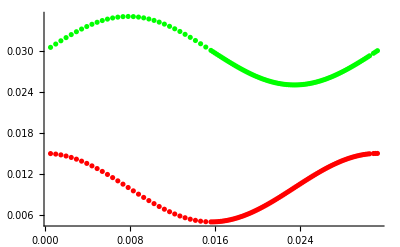

```mathematica
Show[ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Red],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green],PlotRange->Full]
```

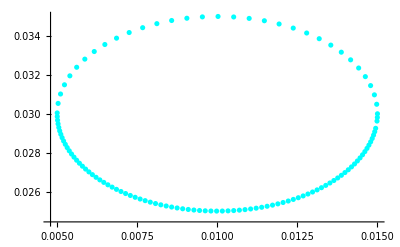

```mathematica
ListPlot[Table[{t[[i,2]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Cyan]
```

```mathematica
(*check U*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_smooth_test_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_sm_test_126.csv not found during Import.

Part::take: Cannot take positions 2 through -1 in $Failed.

Part::partw: Part 3 of 2;;All does not exist.

{{$Failed⟦2;;All⟧⟦2,3⟧,2,All}}

```mathematica
Min[Table[t[[i,2]],{i,1,Length[t]}]]
Max[Table[t[[i,2]],{i,1,Length[t]}]]
Min[Table[t[[i,3]],{i,1,Length[t]}]]
Max[Table[t[[i,3]],{i,1,Length[t]}]]
```

2

2

All

All

```mathematica
Show[ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Red],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green],PlotRange->Full]
```

-Graphics-

```mathematica
(*check nu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/nu_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

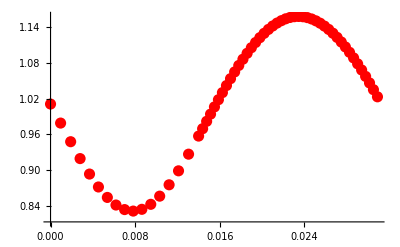

```mathematica
plotnumν=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check psi*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/dpsi_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],norm[t[[i,1]]]},{i,2,Length[t]}]
```

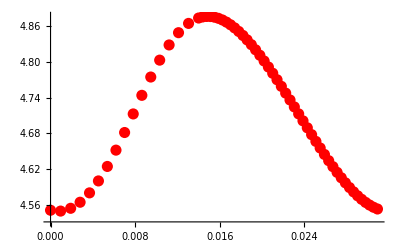

```mathematica
plotnumψ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check mu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/mu_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.0185819,100.458},{0.0201883,99.6995},{0.0177919,100.866},{0.0210011,99.4098},{0.0170129,101.246},{0.0218178,99.206},{0.0162464,101.537},{0.0226364,99.0968},{0.0154937,101.779},{0.0234551,99.0826},{0.0147559,101.74},{0.0242718,99.1655},{0.0139962,101.699},{0.0250847,99.3224},{0.0120977,100.558},{0.0258919,99.5391},{0.0103166,98.82},{0.0266916,99.8015},{0.00863138,97.7131},{0.0274822,100.096},{0.00700083,97.8353},{0.0282619,100.408},{0.0053703,99.0519},{0.0290294,100.723},{0.00368472,100.683},{0.0297833,101.029},{0.00190182,101.652},{0.0305225,101.282},{0.0312836,101.555}}

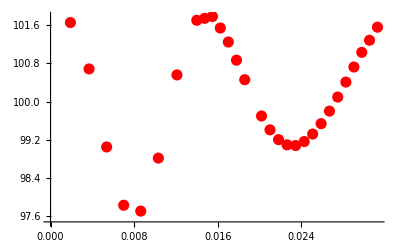

```mathematica
plotnumμ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```